```mathematica
Get["new1through5Sequential.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["OG_Josh_o1through4.m"]
```

```mathematica
For[k = 0, k ≤4,k++,
Josh[k] = Exp[γ  (y  - x)]* Sum[(-1/2)^j (γ)^(2j) * o[j], {j, 0, k}]
]
```

```mathematica
Clear[o]
```

```mathematica
GaussianApprox= (2 π x (1-x) t)^(-1/2) Exp[-(y-(x+2Ne α Λ x (1-x) t / W))^2 / (2 x (1-x) t)]
```

(ⅇ^(-(-x+y-(2 Ne t (1-x) x α Λ)/W)^2/(2 t (1-x) x)))/(√(2 π) √(t (1-x) x))

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,10];
```

```mathematica
kimplot = Kimura[x,y,t,n];
```

```mathematica
Plot[Evaluate[Table[kimplot /. {x-> 0.25, t-> 0.1}, {n,1,11,2}]],{y,0,1},PlotLegends->{Table[n,{n,1,11,2}]},
PlotLabels->Table[TextString[n],{n,1,11,2}], PlotStyle-> ColorData[{"StarryNightColors",{1,6}}]]
```

-Graphics-

```mathematica
kthkimura[x_,y_,t_,m_] := 4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t];
```

```mathematica
kythplot = kthkimura[x,y,t,n];
```

```mathematica
Plot[Evaluate[Table[kythplot /. {x-> 0.25, t-> 0.1}, {n,1,5}]],{y,0,1},PlotLegends->{Table[n,{n,1,5}]},
PlotLabels->Table[TextString[n],{n,1,5}]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\firstkkimura.svg",%15,"SVG"]
```

C:\Users\natha\Documents\firstkkimura.svg

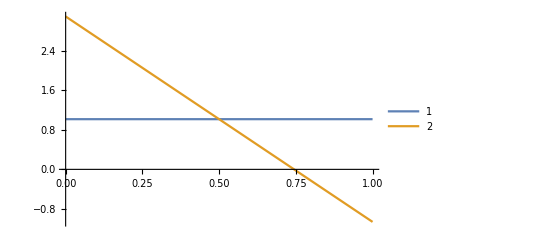

```mathematica
Plot[{Kimura[x,y,t,1] /. {x-> 0.25, t-> 0.1},Kimura[x,y,t,2] /. {x-> 0.25, t-> 0.1}},{y,0,1},PlotLegends->{"1","2"}]
```

```mathematica
Plot[Evaluate[Table[kimplot /. {x-> 0.25, t-> 0.1}, {n,1,5}]],{y,0,1},PlotLegends->{Table[n,{n,1,5}]},
PlotLabels->Table[TextString[n],{n,1,5}]]
```

-Graphics-

```mathematica
Clear[Anim];
Anim=Table[Plot[Evaluate[kimplot/. {x->0.25,t-> 0.1,n->bigN}],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"n=",bigN}, 
PlotRange->{{0,1},{0,5}}],{bigN,1,15}]
```

```mathematica
Export["neutralConvergence.gif",Anim,"DisplayDurations"->0.75]
```

neutralConvergence.gif

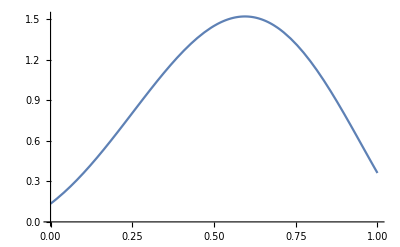

```mathematica
Plot[Evaluate[SimplifiedHayward[3]/.{x->0.5, t->0.25,Ne->500,α->.001,Λ->1,W->1, VG->0.0001111}],{y,0,1}]
```

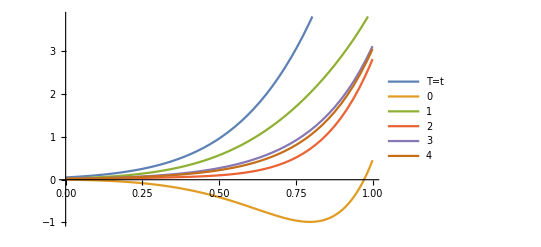

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5, t->0.5,Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

```mathematica
Table[TextString[k],{k,0,5}]
```

{0,1,2,3,4,5}

```mathematica
First[{"0","1","2","3","4","5"}]
```

0

```mathematica
Clear[Anim]
```

```mathematica
NumberForm
```

```mathematica
Anim=Table[Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5,t-> 0.1,Ne->500, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"α=",NumberForm[α, {6,5}]}, 
PlotLabels->Table[TextString[k],{k,0,5}],
PlotRange->{{0,1},{0,10}}],{α,.0001,.01,.00025}];
```

```mathematica
Export["selectionConvergence.gif",Anim,"DisplayDurations"->0.3]
```

selectionConvergence.gif

```mathematica
Length[Anim]
```

40

```mathematica
Anim[[40]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\BigAlphaConvergence.svg",%59,"SVG"]
```

C:\Users\natha\Documents\BigAlphaConvergence.svg

```mathematica
Anim=Table[Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->0.5,Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"T=",t}, 
PlotLabels->Table[TextString[k],{k,0,5}],
PlotRange->{{0,1},{-10,10}}],{t,.001,.5,.025}];
```

```mathematica
Export["TimeConvergence.gif",Anim,"DisplayDurations"->0.75]
```

TimeConvergence.gif

```mathematica
Anim[[1]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\smallTimeConvergence.svg",%37,"SVG"]
```

C:\Users\natha\Documents\smallTimeConvergence.svg

```mathematica
Length[Anim]
```

20

```mathematica
Anim[[20]]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\longTimeConvergence.svg",%40,"SVG"]
```

C:\Users\natha\Documents\longTimeConvergence.svg

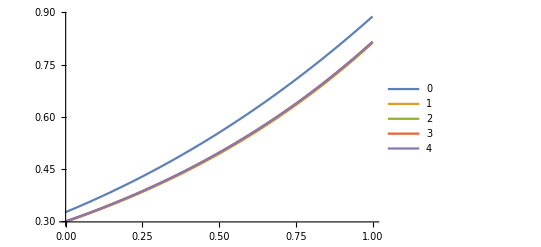

```mathematica
Plot[Evaluate[Table[Josh[k]/. {x->0.5, t->1,γ->1},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,4}]}]
```

```mathematica
Clear[blah];
blah=NDSolve[{D[g[x,t],t] == -(2 Ne α Λ / W) Exp[2 Ne VG t / W]*x*(1-x)*D[g[x,t],x]+1/2*x*(1-x)*D[g[x,t],{x,2}],
g[x,0]==Evaluate[PDF[TriangularDistribution[{0.4999,0.5001},0.5],x]x(1-x)],
g[0,t]==0,
g[1,t]==0}/.{α->.005,Λ->1,W->1, VG->0.00001111, Ne ->500},
g,{x,0,1},{t,0.001,1},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
Plot[{SimplifiedHayward[2] /. {x->0.5,t -> 0.001, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111}, GaussianApprox/. {x->0.5,t -> 0.001, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},
g[x,t] /(x(1-x)) /.blah /.{t->0.001, x->y}}, {y,0,1}, PlotLabels->{"Perturb", "Gaussian", "Numerical"}]
```

-Graphics-

```mathematica
tmp[y_,t_] = Evaluate[GaussianApprox /. {x->0.5, Ne->500,α->0.005, Λ -> 1, W->1}];
joshtmp[y_,t_] = Evaluate[Josh[3]/.{x->0.5,γ->5}];
haywardtmp[y_,t_,VG_] = Evaluate[SimplifiedHayward[3]/. {x->0.5,Ne->500,α->0.005, Λ -> 1, W->1}];
```

```mathematica
Clear[Anim];
Anim=Table[Plot[{haywardtmp[y,t,0.00001111],joshtmp[y,t],tmp[y,t]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"T=",t}, 
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotRange->{{0,1},{-5,5}}],
{t,.001,.5,.025}]
```

```mathematica
Export["TimeComparison.gif",Anim,"DisplayDurations"->0.75]
```

```mathematica
Plot[{haywardtmp[y,0.25,0.00001111],joshtmp[y,0.25],tmp[y,0.25]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotLegends->TextString@Row@{"T=",0.25}, 
PlotRange->{{0,1},{-1,4}}]
```

-Graphics-

```mathematica
Clear[Anim];
Anim=Table[Plot[{haywardtmp[y,0.1,VG],joshtmp[y,0.1],tmp[y,0.1]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->TextString@Row@{"VG=",NumberForm[VG, {6,5}]}, 
PlotLabels->{"Hayward","Josh", "Gaussian"},
PlotRange->{{0,1},{0,10}}],
{VG,.000011111,.11111, 0.005}]
```

```mathematica
Export["VGComparison.gif",Anim,"DisplayDurations"->0.75]
```

VGComparison.gif

```mathematica
Export["C:\\Users\\natha\\Documents\\25gencomparison.svg",%59,"SVG"]
```

C:\Users\natha\Documents\25gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\10gencomparison.svg",%54,"SVG"]
```

C:\Users\natha\Documents\10gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\5gencomparison.svg",%51,"SVG"]
```

C:\Users\natha\Documents\5gencomparison.svg

```mathematica
Export["C:\\Users\\natha\\Documents\\1gencomparison.svg",%43,"SVG"]
```

C:\Users\natha\Documents\1gencomparison.svg

```mathematica
Manipulate[Plot[tmp[y,t], {y,0,1}], {t,0.01,1}]
```

```mathematica
Manipulate[Plot[joshtmp[y,t],{y,0,1}],{t,0.01,1}]
```

```mathematica
Manipulate[Plot[haywardtmp[y,t,VG],{y,0,1}],{t,0.01,1},{VG,.0000011111,.11111}, ContinuousAction->False]
```

```mathematica
Manipulate[Plot[{joshtmp[y,t],tmp[y,t]},{y,0,1},PlotLabels->{"Josh", "Gaussian"}],{t,0.01,1}]
```

```mathematica
Manipulate[Plot[{haywardtmp[y,t,VG],joshtmp[y,t],tmp[y,t]},{y,0,1},PlotLabels->{"Hayward","Josh", "Gaussian"}],{t,0.01,1},{VG,.0000011111000001,.11111000001}, ContinuousAction->False]
```

```mathematica
2 20000 .005^2
```

1.

```mathematica
2 500 0.00025
```

0.25

```mathematica
l = {}
```

{}

```mathematica
Do[AppendTo[l,{i,j,i+j}];
Print[l],{i,{1,2,3}},{j,{1,2,3}}]
```

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5}}

{{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6},{1,1,2},{1,2,3},{1,3,4},{2,1,3},{2,2,4},{2,3,5},{3,1,4},{3,2,5},{3,3,6}}

```mathematica
1/20000
```

1/20000

```mathematica
N[1/20000]
```

0.00005

```mathematica
Clear[out];
out = {{"alpha","VG","expectation","thresh","totalP","Pdetected","Pnotdetected
"}};
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
```

```mathematica
out
```

{{alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
}}

```mathematica
Do[Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected];
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025];
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}];
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}];
Print[expectation];
expectation  = expectation[[1]][[1]];
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}];
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
If[Length[thresh] != 1,Throw[{α, VG, thresh}]];
Ψ = Ψ /. thresh;
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}];
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}];
AppendTo[out,{α,VG,expectation,Ψ[[1]],totalP,Pdetected,Pnotdetected}],
{α, {0.00025, 0.0005, 0.00075,0.001,0.002,0.005}},
{VG, {.101, .0101, .00101}}
]
```

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.472651}}

{0.472651}

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.472651}}

{0.472651}

{{0.0868252}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{Ψ→0.472651}}

{0.472651}

{{0.0867269}}

{{Ψ→0.472537}}

{0.472537}

{{0.0867269}}

{{Ψ→0.472537}}

{0.472537}

{{0.0867269}}

{{Ψ→0.472537}}

{0.472537}

{{0.0865633}}

{{Ψ→0.472346}}

{0.472346}

{{0.0865633}}

{{Ψ→0.472346}}

{0.472346}

{{0.0865633}}

{{Ψ→0.472346}}

{0.472346}

{{0.0863348}}

{{Ψ→0.472079}}

{0.472079}

{{0.0863348}}

{{Ψ→0.472079}}

{0.472079}

{{0.0863348}}

{{Ψ→0.472079}}

{0.472079}

{{0.0847821}}

{{Ψ→0.470244}}

{0.470244}

{{0.0847821}}

{{Ψ→0.470244}}

{0.470244}

{{0.0847821}}

{{Ψ→0.470244}}

{0.470244}

{{0.0746142}}

{{Ψ→0.457218}}

{0.457218}

{{0.0746142}}

{{Ψ→0.457218}}

{0.457218}

{{0.0746142}}

{{Ψ→0.457218}}

{0.457218}

```mathematica
out
```

{{alpha,VG,expectation,thresh,totalP,Pdetected,Pnotdetected
},{0.00025,0.101,0.0868252,0.472651,0.526846,0.0100437,0.516802},{0.00025,0.0101,0.0868252,0.472651,0.531245,0.0104841,0.520761},{0.00025,0.00101,0.0868252,0.472651,0.53552,0.0112951,0.524225},{0.0005,0.101,0.0867269,0.472537,0.527222,0.0100875,0.517135},{0.0005,0.0101,0.0867269,0.472537,0.536023,0.0109891,0.525034},{0.0005,0.00101,0.0867269,0.472537,0.544544,0.0127323,0.531811},{0.00075,0.101,0.0865633,0.472346,0.527322,0.0101315,0.517191},{0.00075,0.0101,0.0865633,0.472346,0.540522,0.0115153,0.529007},{0.00075,0.00101,0.0865633,0.472346,0.553255,0.014323,0.538932},{0.001,0.101,0.0863348,0.472079,0.527146,0.0101756,0.516971},{0.001,0.0101,0.0863348,0.472079,0.544738,0.0120627,0.532676},{0.001,0.00101,0.0863348,0.472079,0.561644,0.0160787,0.545565},{0.002,0.101,0.0847821,0.470244,0.523666,0.0103516,0.513315},{0.002,0.0101,0.0847821,0.470244,0.558678,0.0144629,0.544215},{0.002,0.00101,0.0847821,0.470244,0.591853,0.0249896,0.566864},{0.005,0.101,0.0746142,0.457218,0.486859,0.0108527,0.476006},{0.005,0.0101,0.0746142,0.457218,0.570352,0.0234055,0.546947},{0.005,0.00101,0.0746142,0.457218,0.648419,0.0754103,0.573009}}

```mathematica
Export["alpha_VG.csv",out,"csv"];
```

```mathematica
Clear[out]
```

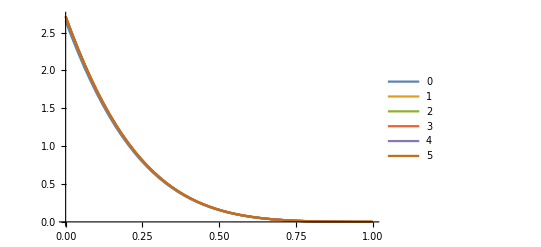

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

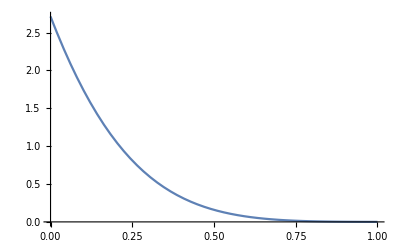

```mathematica
Plot[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y,0,1}]
```

```mathematica
totalP = Integrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, 0.00001,.9999}]
```

6.87861×10^159

```mathematica
Pdetected = Integrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, Min[expectation+Ψ,1],1}]
```

-1.37572×10^160

```mathematica
Pnotdetected = Integrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

6.87861×10^159

```mathematica
totalP = NIntegrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, 0,1}]
```

0.526846

```mathematica
Pdetected = NIntegrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, Min[expectation+Ψ,1],1}]
```

0.0100437

```mathematica
Pnotdetected = NIntegrate[Evaluate[SimplifiedHayward[3]/. {x->expectation,t -> time, Ne->selectedNe,α->0.00025, Λ -> 1, W->1, VG->.101}],{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.516802

```mathematica
{α, {0.00025, 0.0005, 0.00075,0.001,0.002,0.005}},
{VG, {.101, .0101, .00101}
```

```mathematica
Clear[blah];
Clear[Ne];
blah=NDSolve[{0 == ( SourceNe α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{α->.005,Λ->1,W->1, θ ->.5, SourceNe -> 20000},
g,{x,0,1},MaxStepSize->.000025];
```

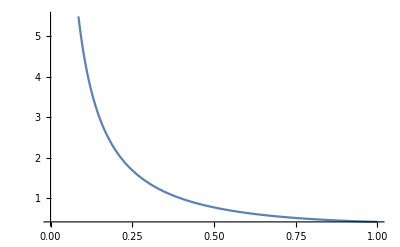

```mathematica
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
```

```mathematica
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.52598}

```mathematica
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
```

{{0.0746142}}

```mathematica
expectation  = expectation[[1]][[1]]
```

0.0408214

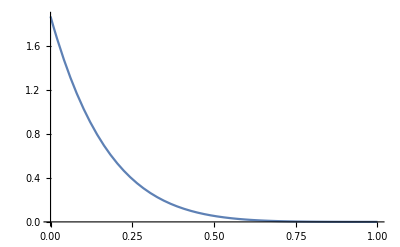

```mathematica
Plot[neutral/. {x->expectation, t->.25}, {y,0,1}]
```

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->.25}], {y,0,1}]
```

0.292025

```mathematica
pNeutFix = 1- neutAUC
```

0.707975

```mathematica
.99 - pNeutFix
```

0.282025

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->.25}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}];
```

```mathematica
thresh = Solve[tmp == (0.99 - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
thresh = {{Ψ->0.394830239061778},{Ψ->0.3}}
```

{{Ψ→0.39483},{Ψ→0.3}}

```mathematica
Length[thresh]
```

2

```mathematica
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
```

Throw::nocatch: Uncaught Throw[{α,VG,{{Ψ→0.39483},{Ψ→0.3}}}] returned to top level.

Hold[Throw[{α,VG,{{Ψ→0.39483},{Ψ→0.3}}}]]

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->.25}],{y, 0, expectation+Ψ}];
```

```mathematica
thresh = Solve[tmp == (0.99 - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

{{Ψ→0.39483}}

```mathematica
Ψ = Ψ /. thresh
```

{0.39483,0.3}

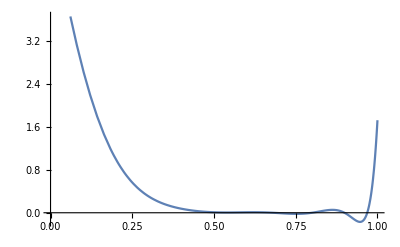

```mathematica
Plot[SimplifiedHayward[3]/.{x->expectation,t -> 0.1, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y,0,1}]
```

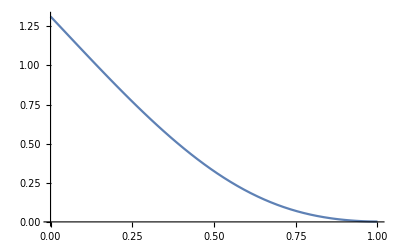

```mathematica
Plot[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y,0,1}]
```

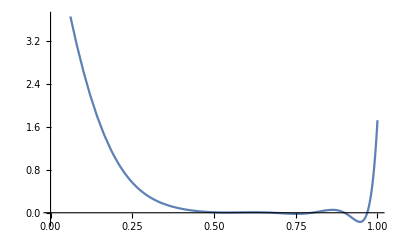

```mathematica
Plot[Evaluate[SimplifiedHayward[5]/.{x->expectation,t -> 0.1, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111}],{y,0,1}]
```

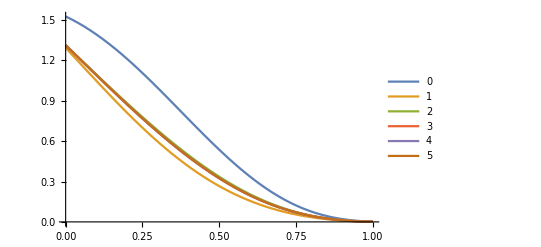

```mathematica
Plot[Evaluate[Table[SimplifiedHayward[k]/. {x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

```mathematica
totalP = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y, 0,1}]
```

0.443845

```mathematica
Pdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y, Min[expectation+Ψ,1],1}]
```

0.0749551

```mathematica
(*Pdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y, Min[expectation+Ψ,1],0.6}]*)
```

0.0497662

```mathematica
Pnotdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> 0.25, Ne->500,α->0.005, Λ -> 1, W->1, VG->.00001111},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.36889

```mathematica
Pdetected + Pnotdetected
```

0.443845

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.25;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.00025;
VG =.101;
```

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

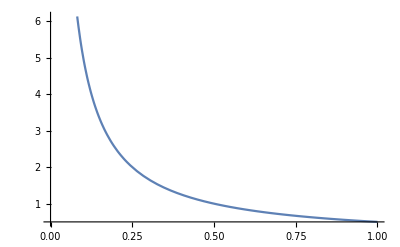

```mathematica
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
```

```mathematica
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
```

{5.75584}

```mathematica
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
```

{{0.0868252}}

```mathematica
Print[expectation]
```

{{0.0868252}}

```mathematica
expectation  = expectation[[1]][[1]]
```

0.0868252

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
```

0.526055

```mathematica
pNeutFix = 1- neutAUC
```

0.473945

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}]
```

-2.7105 Max[0,0.0868252-Ψ]+5.62403 Max[0,0.0868252-Ψ]^2-5.41449 Max[0,0.0868252-Ψ]^3+0.865281 Max[0,0.0868252-Ψ]^4+3.79487 Max[0,0.0868252-Ψ]^5-4.76705 Max[0,0.0868252-Ψ]^6+2.97585 Max[0,0.0868252-Ψ]^7-1.11272 Max[0,0.0868252-Ψ]^8+0.243283 Max[0,0.0868252-Ψ]^9-0.0246171 Max[0,0.0868252-Ψ]^10+2.7105 Min[1,0.0868252+Ψ]-5.62403 Min[1,0.0868252+Ψ]^2+5.41449 Min[1,0.0868252+Ψ]^3-0.865281 Min[1,0.0868252+Ψ]^4-3.79487 Min[1,0.0868252+Ψ]^5+4.76705 Min[1,0.0868252+Ψ]^6-2.97585 Min[1,0.0868252+Ψ]^7+1.11272 Min[1,0.0868252+Ψ]^8-0.243283 Min[1,0.0868252+Ψ]^9+0.0246171 Min[1,0.0868252+Ψ]^10

```mathematica
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.472651}}

```mathematica
Print[thresh]
```

{{Ψ→0.472651}}

```mathematica
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
```

```mathematica
Ψ = Ψ /. thresh
```

{0.472651}

```mathematica
Plot[Evaluate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar}],{y,0,1}]
```

-Graphics-

```mathematica
totalP = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}]
```

0.526846

```mathematica
Pdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}]
```

0.0100437

```mathematica
Pnotdetected = NIntegrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.516802

```mathematica
totalP = Integrate[Evaluate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar}],{y, 0,1}]
Pdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}]
Pnotdetected = Integrate[SimplifiedHayward[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

-6.87861×10^159

-1.37572×10^160

6.87861×10^159